```mathematica
test1=StringSplit[Import["C:\\Users\\Adam Yu\\source\\repos\\PeacefulExpedition\\test1.txt"],"\n"];
test2=StringSplit[Import["C:\\Users\\Adam Yu\\source\\repos\\PeacefulExpedition\\test2.txt"],"\n"];
```

```mathematica
results1=ClassifierMeasurements[c,AssociationThread[#[[1]],#[[2]]]&@Transpose[Partition[test1,2]]//Normal]
```

ClassifierMeasurementsObject[…]

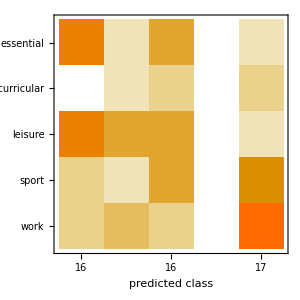

```mathematica
results1["ConfusionMatrixPlot"]
```

```mathematica
{Transpose[Partition[test1,2]][[1]],c[#]&/@Transpose[Partition[test1,2]][[1]],Transpose[Partition[test1,2]][[2]]}//Transpose//TableForm
```

eat apple | leisure | essential
play piano | leisure | extracurricular
play video games | leisure | leisure
finish math homework | work | work
drink wine | essential | essential
play violin | leisure | extracurricular
drink coffee | essential | essential
play badminton | leisure | sport
play tennis | leisure | sport
write essay | work | work
have cheerleading practice | essential | sport
attend club meeting | extracurricular | extracurricular
write symphony | work | extracurricular
write proof for P = NP | leisure | work
prove the Riemann hypothesis | work | work
do psychology homework | work | work
prepare notes for tomorrow | work | work
meditate | extracurricular | leisure
write announcement | essential | work
go horseback riding | work | extracurricular
I'm going to go play ball tomororow  | leisure | sport
I'm going to finish my history work tonight | work | work
I'm going to go gokarting | work | leisure
I'm playing paintball later | leisure | leisure
I'm taking a roadtrip at lunch | essential | leisure
I'm going for a city ride tonight | essential | leisure
I'm spinning my fidget spinner later | essential | leisure
I'm playing my phone games later | leisure | leisure
I'm eating ass | essential | leisure
I'm going to a Hackathon | essential | leisure
I'm reading Spivak calculus | leisure | work
I'm reading Harry Potter later | essential | work
I'm going to the gym to bodybuild | extracurricular | sport
I'm going to buy pizza | leisure | essential
I'm going to the arcade | essential | leisure
I'll be swimming | work | sport
I'll be hoola-hooping | work | sport
Eat a salad | leisure | essential
Eat banana | essential | essential
I'll be consuming slices of pizza | leisure | essential
I'll be going to the atrium to get sushi | extracurricular | essential
drink water | essential | essential
drink champagne | essential | essential
eat ramen | essential | essential
I'll be fencing later | essential | sport
I'll be swordfighting tonight | work | sport
I'll be watching a hockey game | leisure | leisure
I'll be playing in a hockey game | leisure | sport
I'll be reading the AoPS Volume 2 | extracurricular | work
I'll be cooking food | work | essential
I'll be hoolahooping | work | sport
Sailing | work | sport
write emails | work | work
write psychology paper | work | work
Watch lectures on MIT OCW | extracurricular | work
I'll be doing my interview at Google  | extracurricular | work
I'll be watching TV | extracurricular | leisure
I'll be watching a movie | extracurricular | leisure
I'll be listening to music | extracurricular | leisure

```mathematica
(*Plot[Piecewise[{{69LogisticSigmoid[(x-30)/6.9],x≤60},{x/6.9+59.5,x>60}}],{x,0,60*24}]*)
```

```mathematica
(*Export["C:\\Users\\Adam Yu\\source\\repos\\PeacefulExpedition\\sigmoid.csv",Table[Piecewise[{{69LogisticSigmoid[(x-30)/6.9],x≤60},{x/6.9+59.5,x>60}}],{x,0,60*24}]//Round]*)
```